{m[1][0]==-8.73615,x[1][0]==7.7072,m[2][0]==1.09748,x[2][0]==8.4876}

{m[1][0]==-1,m[2][0]==2,x[1][0]==0,x[2][0]==4.9999}

-0.1

0.1

-1.99914

1.00172

-1.99571

-0.501075

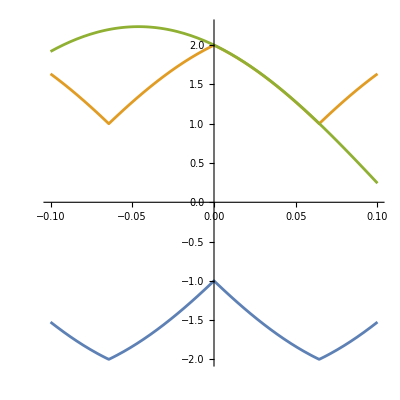

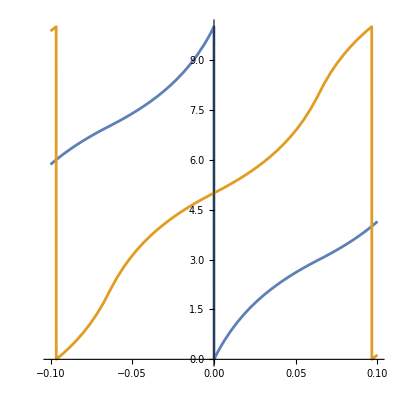

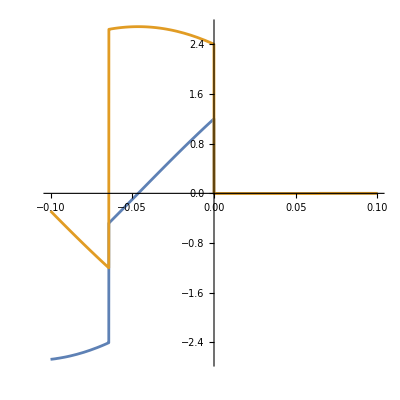

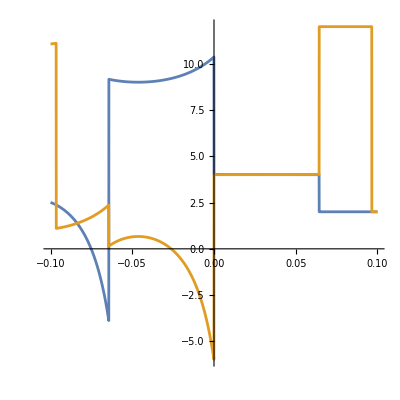

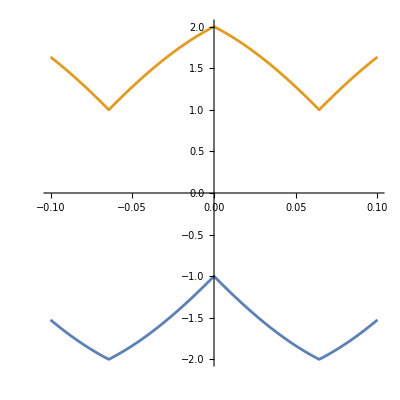

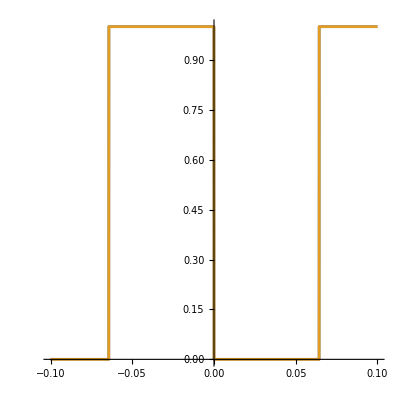

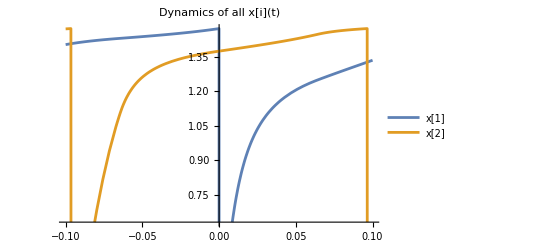

```mathematica
ClearAll["Global`*"];
(*Define the system of equations*)
L=5;  (*Threshold for wrap-around*)

n=2;

uF[xx_,t_]:=Apply[Plus,Table[m[j][t]Abs[Mod[xx-x[j][t]-L,2L]-L],{j,1,n}]]
u[k_,t_]:=Apply[Plus,Table[m[j][t]Abs[Mod[x[k][t]-x[j][t]-L,2L]-L],{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]Sign[Mod[x[k][t]-x[j][t]-L,2L]-L],{j,1,n}]]


(*Define initial conditions*)
initialConditions=Flatten[Table[{m[i][0]==RandomReal[{-10,10}],x[i][0]==RandomReal[{0,2L}]},{i,n}]]
initialConditions=Flatten[{m[1][0]==-1,m[2][0]==2,x[1][0]==0,x[2][0]==4.9999}]

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];
(*Solve the system numerically*)
Tstart=-0.1;
Tend=0.1;
T={t,Tstart,Tend};
S=10^-3;
wrapEvents=Flatten[Table[
With[{i=i},
{
WhenEvent[x[i][t]>2L+S,x[i][t]->0],
WhenEvent[x[i][t]<0-S,x[i][t]->2L]
}],{i,n}
]];

sol=NDSolve[Join[eqns,initialConditions,wrapEvents],Flatten[Table[{m[i],x[i]},{i,n}]],T];
Tstart=Apply[Max,Table[sol[[1,i,2]]["Domain"][[1,1]],{i,1,2n}]]
Tend=Apply[Min,Table[sol[[1,i,2]]["Domain"][[1,2]],{i,1,2n}]]
T={t,Tstart,Tend};

XD[i_,t_]=m[i][t];
Circ[a_,r_]:={r Cos[2Pi a /L],r Sin[2Pi a /L]};
Circ[a_,r_]:={r Cos[2Pi a /L],r Sin[2Pi a /L]};

(*Plot3D[uF[x,t]/.sol[[1]],{x,0,10},{t,Tstart,Tend}]*)
(*ParametricPlot[Evaluate[Table[{t,-m[i][t]ux[i,t]u[i,t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]

ParametricPlot[Evaluate[Table[{t,m[i][t]M}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]*)
(*ParametricPlot[Evaluate[{t,-m[2][t]u[2,t]ux[2,t]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,-m[2][t]m[1][t]^2(Mod[x[2][t]-x[1][t]-L,2L]-L)}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]*)
(*ParametricPlot[Evaluate[Table[{t,u[2,t]^2}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,m[1][t]^2(Mod[x[2][t]-x[1][t]-L,2L]-L)^2}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]*)
(*dm[i_]:=-m[i][t]ux[i,t]u[i,t];
dx[i_]:=u[i,t]^2;
ParametricPlot[Evaluate[Table[{t,(m[1][t]m[2][t])(Abs[Mod[x[2][t]-x[1][t]-L,2L]-L])}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,(dm[1]m[2][t]+dm[2]m[1][t])(Abs[Mod[x[2][t]-x[1][t]-L,2L]-L])+Sign[Mod[x[2][t]-x[1][t]-L,2L]-L]m[1][t]m[2][t](dx[2]-dx[1])}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]*)

(*M2=m[1][t]m[2][t]Abs[Mod[x[2][t]-x[1][t]-L,2L]-L];
M1=(m[1][t]^2+m[2][t]^2);
p[1]=ArcTan[m[1][0],m[2][0]];
p[2]=ArcTan[m[1][0],m[2][0]]+Pi/2;
ParametricPlot[Evaluate[{t,M2}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,m[i][t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,Sqrt[M1]Sin[M2 t+p[i]]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]*)

time=0.06444;
m[1][time]/.sol[[1]]
m[2][time]/.sol[[1]]
m[1][time]/m[2][time]/.sol[[1]]
m[2][time]/m[1][time]/.sol[[1]]

M1=(m[1][t]^2+m[2][t]^2);
M2=m[1][t]m[2][t]Abs[Mod[x[2][t]-x[1][t]-L,2L]-L];
SP=Max[0,+Sign[Mod[x[2][t]-x[1][t]-L,2L]-L]];
SM=Max[0,-Sign[Mod[x[2][t]-x[1][t]-L,2L]-L]];
initT=0.06444;
ph[1]=ArcTan[m[2][initT],m[1][initT]]-initT M2;
ph[2]=ArcTan[m[2][initT],m[1][initT]]-initT M2+Pi/2;
th[1]=ArcTan[m[1][initT],m[2][initT]]-initT M2;
th[2]=ArcTan[m[1][initT],m[2][initT]]-initT M2-Pi/2;
xF[i_]:=-(M2/M1)(Cot[M2 t+ph[i]]-Cot[p[i]])+x[i][0];
mF[i_]:=Sqrt[M1](SP Sin[M2 t+ph[i]]+SM Cos[M2 t+th[i]]);
xF[i_]:=-(M2/M1)(SP Cot[M2 t+ph[i]]-SM Tan[M2 t+th[i]]);
DynamicModule[{a},Column[{Dynamic@Plot[
Evaluate[m[2][t]-Sqrt[M1](SM Cos[M2 t+a])/.sol[[1]]]
,{t,Tstart,Tend},PlotLegends->Table["a=["<>ToString[a]<>"]",{i,n}],PlotRange->{All,{-1,1}}],Slider[Dynamic@a,{0,4}]}]]
DynamicModule[{a},Column[{Dynamic@Plot[
Evaluate[m[1][t]-Sqrt[M1](SM Cos[M2 t+a])/.sol[[1]]]
,{t,Tstart,Tend},PlotLegends->Table["a=["<>ToString[a]<>"]",{i,n}],PlotRange->{All,{-1,1}}],Slider[Dynamic@a,{0,4}]}]]
Plot[Evaluate[{
m[1][t],
m[2][t],
Sqrt[M1]Sin[M2 t+ph[2]]
}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
Plot[Evaluate[Table[x[i][t]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
Plot[Evaluate[Table[m[i][t]-mF[i]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
Plot[Evaluate[Table[x[i][t]-xF[i]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
Plot[Evaluate[Table[m[i][t]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
Plot[Evaluate[Table[SM/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]


(*ParametricPlot[Evaluate[{t,M}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,-m[2][t]u[2,t]ux[2,t]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,-m[2][t]m[1][t]^2(Mod[x[2][t]-x[1][t]-L,2L]-L)}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,-m[1][t]M Sign[Mod[x[2][t]-x[1][t]-L,2L]-L]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]

ParametricPlot[Evaluate[{t,-m[1][t]u[1,t]ux[1,t]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,m[1][t]m[2][t]^2(Mod[x[2][t]-x[1][t]-L,2L]-L)}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,m[2][t]M Sign[Mod[x[2][t]-x[1][t]-L,2L]-L]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]*)

(*
ParametricPlot[Evaluate[Table[{t,x[i][t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,m[i][t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
plotM1=ParametricPlot[Evaluate[{t,m[1][t]m[2][t]Abs[Mod[x[2][t]-x[1][t]-L,2L]-L]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1];
plotM2=ParametricPlot[Evaluate[{t,m[1][t]^2+m[2][t]^2}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1];

pp=ParametricPlot[Evaluate[Table[Circ[x[i][t],i]/.sol[[1]],{i,n}]],{t,Tstart,Tend},ColorFunction->Function[{t},Hue[t]]]
plotRange1={{-1,1},{-1,1}};
plotRange1=AbsoluteOptions[pp,PlotRange][[1]][[2]]
Manipulate[Graphics[Point[Evaluate[Table[Circ[x[i][d],XD[i,d]]/.sol[[1]],{i,n}]]],Axes->True,PlotRange->plotRange1],{d,Tstart,Tend}]*)

plotX=Plot[Evaluate[Table[ArcTan[x[i][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]
```